# Maze Tracer

## File Header

Version: 0.1 SMB
Version Date: 07-17-2018
Version Author: Shannon Brownlee

## Description

This is a game in which the player must use their cursor to drag a circle, called the locator, from a specified start point to a specified finish point along a specified path. While the player does that, the path the player takes is being sampled and stored in a list of coordinate pairs. Upon reaching the finish point, data that was collected is graphed to give the user feedback on hand-eye coordination.

## Designer Intention

### Why Maze Tracer?

Maze Tracer is designed to be the first of several interactive exercises to help STEM students internalize engineering principles.
This version is a proof of concept intended to track a cursor-dragged object along a specified path.
The final design would incorporate additional features that illustrate the engineering concept State of Control: variation from equilibrium has non-linear effects on the control of the system.

### Application Design

Data acquisition done with Table function sampling Locator position independently with regular Pause intervals. 
User interface uses built-in functionality from LocatorPane.

## Possible Next Steps

Add a specific Variability or Noise function

## Instructions

1. Run the Global Variable Initialization
2. Run the User Interface section code: this generates the LocatorPane
3. Begin Data Acquisition: this starts a counter and collects 10 data points from the locator in the LocatorPane, one per second (see section: User Interface)
3. Use the User Interface section: drag the locator along blue line from “start” to “finish”
4. When data acquisition is complete, there will be a graph displaying the collected data points

## Initialize Global Variables

```mathematica
locatorCoord = {0.2,3}; (*sets the start point of the locator at (0, 1.5)*)
lengthFactor = 3; (*length of the game window/LocatorPane*)
testDuration = 20; (*sets the number of seconds during which data is collected*)
numSamples = 20; (*must be an integer >0; sets the number of data samples which will be collected*)
samplingInterval = testDuration/numSamples;(*sets the number of seconds between data sampling*)
```

## User Interface

Possible Concern: Image Size may different for computers with different resolutions

```mathematica
LocatorPane[Dynamic[locatorCoord], (*defines locatorCoord as the value that is dynamically updating with locator icon position*)
Graphics[{
Lighter[Gray,0.5],Rectangle[{0,0},{16,6}], (*grey background*)
Thin,Cyan, Rectangle[{0,2.8},{16,3.2}], (*blue line*)
Text[Style["finish",Red,16.],{15.5,3.35}], (*red finish*)
Text[Style["start",Red,16],{0.5,3.35}] (*red start*)
},
ImageSize->600]]
```

## Data Acquisition

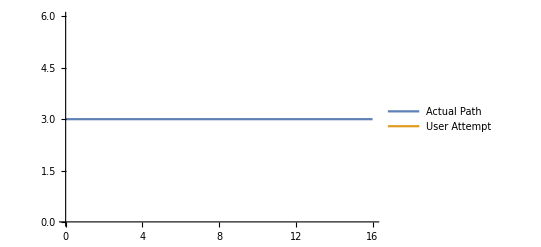

```mathematica
tracePath=Table[Pause[samplingInterval];locatorCoord,numSamples];
 (*generates a table of coordinate points/data which are collected during gameplay*)
linePath=Table[{x,3},{x,0,16,1}]; 
(*actual path*)
ListLinePlot[{linePath,tracePath},PlotLegends->{"Actual Path","User Attempt"},PlotRange-> {All,{0,6}}]
(*plots the collected data points on a graph*)
```

## Multiple Levels

### Level 2

```mathematica
LocatorPane[Dynamic[locatorCoord], (*defines locatorCoord as the value that is dynamically updating with locator icon position*)
Graphics[{
Lighter[Gray,0.5],Rectangle[{0,0},{16,6}], (*grey background*)
Thin,Cyan, Rectangle[{0,2.8},{4,3.2}], (*blue line*)
Thin,Cyan,Rectangle[{4,2.8},{4.4,4.2}],
Thin,Cyan,Rectangle[{4,4.2},{10,4.6}],
Thin,Cyan,Rectangle[{10,2},{10.4,4.6}],
Thin,Cyan,Rectangle[{10,2},{16,2.4}],
Text[Style["finish",Red,16],{15.5,2.65}], (*red finish*)
Text[Style["start",Red,16],{0.5,3.35}] (*red start*)
},
ImageSize->600]]
```

### Level 3

```mathematica
LocatorPane[Dynamic[locatorCoord], (*defines locatorCoord as the value that is dynamically updating with locator icon position*)
Graphics[{
Lighter[Gray,0.5],Rectangle[{0,0},{16,6}], (*grey background*)
Thin,Cyan, Rectangle[{0,2.8},{4,3.2}], (*blue line*)
Thin,Cyan,Rectangle[{4,2.8},{4.4,4.8}],
Thin,Cyan,Rectangle[{4,4.8},{6,5.2}],
Thin,Cyan,Rectangle[{6,0.8},{6.4,5.2}],
Thin,Cyan,Rectangle[{6.4,0.8},{8,1.2}],
Thin,Cyan,Rectangle[{8,0.8},{8.4,3.8}],
Thin,Cyan,Rectangle[{8,3.8},{16,4.2}],
Text[Style["finish",Red,16],{15.5,4.4}], (*red finish*)
Text[Style["start",Red,16],{0.5,3.35}] (*red start*)
},
ImageSize->600]]
```

### Level 4

```mathematica
LocatorPane[Dynamic[locatorCoord], (*defines locatorCoord as the value that is dynamically updating with locator icon position*)
Graphics[{
Lighter[Gray,0.5],Rectangle[{0,0},{16,6}], (*grey background*)
Thin,Cyan, Rectangle[{0,2.8},{4,3.2}], (*blue line*)
Thin,Cyan,Rectangle[{4,2.8},{4.4,4.8}],
Thin,Cyan,Rectangle[{4,4.8},{5.8,5.2}],
Thin,Cyan,Rectangle[{5.8,0.6},{6.2,5.2}],
Thin,Cyan,Rectangle[{6.2,0.6},{8,1}],
Thin,Cyan,Rectangle[{7.6,0.8},{8,4.2}],
Thin,Cyan,Rectangle[{8,3.8},{9,4.2}],
Thin,Cyan,Rectangle[{8.6,2},{9,4.2}],
Thin,Cyan,Rectangle[{8.6,1.6},{16,2}],
Text[Style["finish",Red,16],{15.5,2.2}], (*red finish*)
Text[Style["start",Red,16],{0.5,3.35}] (*red start*)
},
ImageSize->600]]
```

## Putting It All Together

```mathematica
Button["Start",locatorCoord = {0.2,3}; (*sets the start point of the locator at (0, 1.5)*)
lengthFactor = 3; (*length of the game window/LocatorPane*)
testDuration = 20; (*sets the number of seconds during which data is collected*)
numSamples = 20; (*must be an integer >0; sets the number of data samples which will be collected*)
samplingInterval = testDuration/numSamples;(*sets the number of seconds between data sampling*)]
```

Start

```mathematica
Button["Level 1",
{
LocatorPane[Dynamic[locatorCoord], (*defines locatorCoord as the value that is dynamically updating with locator icon position*)
Graphics[{
Lighter[Gray,0.5],Rectangle[{0,0},{16,6}], (*grey background*)
Thin,Cyan, Rectangle[{0,2.8},{16,3.2}], (*blue line*)
Text[Style["finish",Red,16.],{15.5,3.35}], (*red finish*)
Text[Style["start",Red,16],{0.5,3.35}] (*red start*)
},
ImageSize->600]],
tracePath=Table[Pause[samplingInterval];locatorCoord,numSamples];
 (*generates a table of coordinate points/data which are collected during gameplay*)
linePath=Table[{x,3},{x,0,16,1}]; 
(*actual path*)
ListLinePlot[{linePath,tracePath},PlotLegends->{"Actual Path","User Attempt"},PlotRange-> {All,{0,6}}]
(*plots the collected data points on a graph*)}]
```

Level 1

```mathematica
Button["Level 2"
```

```mathematica
Button["Level 3"
```

```mathematica
Button["Level 4"
```

## Project Reflection

### Project Information

Please make sure your name(s) and project title are at the top of the Mathematica notebook in their own cells appropriately styled.

Project Category:

Project Type:

Date of Completion:

### Work and Organization

Please make sure you include a text cell with a project description at the top of your notebook.

Answer Here - If this is a group project, how was the work divided among group members?:

### Project Goals

Did you meet your goals with this project?

How did the project change once you started?

What are the strengths and weaknesses of this project?

Did you share your work with someone or a client? If so, what was the response?

### Learning

How did you learn by doing this project?

What would you do differently if you were to do this project again?

### Mathematics

How did you use mathematics in this project?

### Peer Review

What did your reviewer like about your project?

What was your response to peer review? How did the project change because of review and/or what suggestions did you not take?

### Additional Information

Other thoughts, comments, ideas, etc.?